```mathematica
(*PROGRAM*)
```

```mathematica
Clear["Global`*"]
```

```mathematica
φ[0][x_]:=1;
φ[i_][x_]:=x^i;

aproksymacja [φ_,xa_,ya_,p_,w_]:=Module[{f,n,l,b,i,j,k,a,F},
n=p+1;
l = Length[xa];
f=Table[0,{n}];
For[k=1,k≤n,k++, f[[k]]=∑_(j=1)^l (w[xa[[j]]]*ya[[j]]*φ[(k-1)][xa[[j]]]);];
b=Table[0,{n},{n}];
For[i=1,i≤n,i++,
For[k=1,k≤n,k++,
b[[i,k]]=∑_(j=1)^l (w[xa[[j]]]*φ[i-1][xa[[j]]]*φ[k-1][xa[[j]]]);];];
a=LinearSolve[b,f];
F=0;
For[i=1,i≤Length[a], i++,
F=F+a[[i]]*φ[i-1][x];];
Simplify[F];
Print[F];
Return[F];]
```

```mathematica
(*PROGRAM TESTOWY*)
x1={0,1,2,3};
y1={1,-1,2,4};
w[x_]:=1;
aproksymacja[φ,x1,y1,2,w]
```

7/10-(9 x)/5+x^2

7/10-(9 x)/5+x^2

```mathematica
(*ZADANIE A*)
w1[x_]:=1;
xa={0,1,2,3,4,5,6,7,8,9,10,11,12};
ya={Sin[xa[[1]]],Sin[xa[[2]]],Sin[xa[[3]]],Sin[xa[[4]]],Sin[xa[[5]]],Sin[xa[[6]]],Sin[xa[[7]]],Sin[xa[[8]]],Sin[xa[[9]]],Sin[xa[[10]]],Sin[xa[[11]]],Sin[xa[[12]]],Sin[xa[[13]]]};
ZADA=aproksymacja[φ,xa,ya,3,w1] //N
```

1/4004 x^2 (22 Sin[1]-122 Sin[2]-178 Sin[3]-167 Sin[4]-110 Sin[5]-28 Sin[6]+58 Sin[7]+127 Sin[8]+158 Sin[9]+130 Sin[10]+22 Sin[11]-187 Sin[12])+1/364 (132 Sin[1]+42 Sin[2]-12 Sin[3]-37 Sin[4]-40 Sin[5]-28 Sin[6]-8 Sin[7]+13 Sin[8]+28 Sin[9]+30 Sin[10]+12 Sin[11]-33 Sin[12])+1/3432 x^3 (6 Sin[2]+8 Sin[3]+7 Sin[4]+4 Sin[5]-4 Sin[7]-7 Sin[8]-8 Sin[9]-6 Sin[10]+11 Sin[12])+1/24024 x (-2244 Sin[1]+2670 Sin[2]+4972 Sin[3]+5243 Sin[4]+4064 Sin[5]+2016 Sin[6]-320 Sin[7]-2363 Sin[8]-3532 Sin[9]-3246 Sin[10]-924 Sin[11]+4015 Sin[12])

0.632651-0.443524 x+0.0895692 x^2-0.00525558 x^3

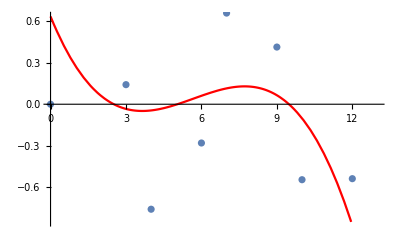

```mathematica
Print[Show[Plot[ZADA,{x,0,13},PlotStyle->Red], ListPlot[Thread[{xa,ya}]]]];
```

```mathematica
w2[x_]:=10/; 3<= x <= 7;
w2[x_]:=10^-10
{w2[0], w2[1], w2[3],w2[4], w2[5], w2[6], w2[7], w2[8], w2[9], w2[10], w2[11], w2[12]}
ZADA2 =aproksymacja[φ, xa, ya,3, w2]//N
```

{1/10000000000,1/10000000000,10,10,10,10,10,1/10000000000,1/10000000000,1/10000000000,1/10000000000,1/10000000000}

(7056000122902740004245055500006660462 Sin[1]+2436000054667190001717941749996890447 Sin[2]+23600001328555000018669879999122164400000000000 Sin[3]-33150000658336250054416570001111262100000000000 Sin[4]-5400001028073000067014410001087902200000000000 Sin[5]+28099999685226499961327124999115576700000000000 Sin[6]-11399999052555999988941200000577492800000000000 Sin[7]-2026499977755387499373686200002437781 Sin[8]-6243999970178399999035043699999599466 Sin[9]-13553999973135779999068976849998026657 Sin[10]-24743999991968709999670977999998486028 Sin[11]-40601500032018372501036539500001744253 Sin[12])/1750000212021750325471487511202389400024555087+(x^2 (3745000040076305000285330149996857041 Sin[1]+1260000016809419998953295599988146224 Sin[2]+9750000319754499854287679998413929800000000000 Sin[3]-18000000283367000118065680001616110800000000000 Sin[4]-1000000335857500045203575001375236500000000000 Sin[5]+16999999954848000049400939999036815600000000000 Sin[6]-7749999618685499857725190000479691600000000000 Sin[7]-1189999992638929997900550200000244952 Sin[8]-3604999991882094997710616049996973323 Sin[9]-7759999995990699998242179999995979400 Sin[10]-14092500007039094999729972599998260554 Sin[11]-23040000027101630002408724400004814156 Sin[12]))/7000000848087001301885950044809557600098220348+(x^3 (-735000005608574999994965249999488755 Sin[1]-245000002284484999793053049998288227 Sin[2]-1750000038544499974462479999777845800000000000 Sin[3]+3500000041319500019094280000219385800000000000 Sin[4]+43608500005427305000178202700000000000 Sin[5]-3499999999212500011401074999886064500000000000 Sin[6]+1749999945321499972671470000041914800000000000 Sin[7]+244999999096754999617072699999774712 Sin[8]+734999999263144999597686549999359353 Sin[9]+1575000000277034999709179549999326377 Sin[10]+2852500002463074999992174999999829090 Sin[11]+4655000006145915000487296200001020798 Sin[12]))/21000002544261003905657850134428672800294661044+(x (-54810000769181730014673894899966095686 Sin[1]-18655000331633574992625018749814727185 Sin[2]-159500007071738998336555759973871695600000000000 Sin[3]+263500004990796501614417360027704136600000000000 Sin[4]+30000006658363000894385990024765414600000000000 Sin[5]-233499998434925500192681364981177225100000000000 Sin[6]+99499993345044998657183800011386854000000000000 Sin[7]+16554999856323884977479499900039682884 Sin[8]+50609999820612189973835857099980777146 Sin[9]+109424999862656504978680594649952257691 Sin[10]+199265000018797969995053397599969230884 Sin[11]+326395000325377725025993951000046803090 Sin[12]))/21000002544261003905657850134428672800294661044

10.4317-5.7181 x+0.873654 x^2-0.0365756 x^3

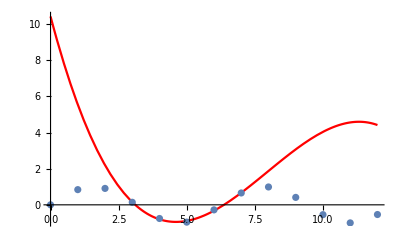

```mathematica
Print[Show[Plot[ZADA2,{x,0,12},PlotStyle->Red], ListPlot[Thread[{xa,ya}]]]];
```

```mathematica
(*ZADANIE B*)
```

```mathematica
t={0,25,50,75,100,125,150};
T={90,80,71,63,57,51,46};
w3[x_]:=1;
dane=Transpose[{t,T}]
```

{{0,90},{25,80},{50,71},{75,63},{100,57},{125,51},{150,46}}

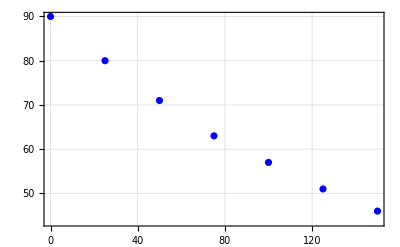

```mathematica
rys=ListPlot[{dane},PlotStyle->Blue,PlotTheme->"Detailed"]
```

```mathematica
logT=Log[T]
```

{Log[90],Log[80],Log[71],Log[63],Log[57],Log[51],Log[46]}

```mathematica
ZADB=aproksymacja[φ,t,logT,1,w3]//N
```

1/700 x (3 Log[46]+2 Log[51]+Log[57]-Log[71]-2 Log[80]-3 Log[90])+1/28 (-5 Log[46]-2 Log[51]+Log[57]+4 Log[63]+7 Log[71]+10 Log[80]+13 Log[90])

4.49162-0.00447648 x

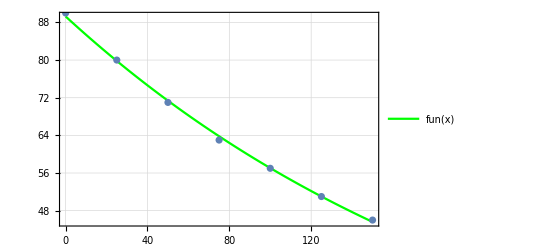

```mathematica
e=4.49162;
f=-0.00447648;
g=Exp[e];
fun[xn_]:=g Exp[f*xn]
Print[Show[Plot[fun[x],{x,t[[1]],t[[Length[t]]]},PlotStyle->Green,PlotTheme->"Detailed"],ListPlot[Thread[{t,T}]]]]
```

```mathematica
Solve[fun[xn]==20,xn]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{xn→334.166}}

```mathematica
fun[334]
```

20.0149

```mathematica
(*Dla t = 334s, T = 20 stopni Celsjusza*)
```